```mathematica
(*
Lista 1 - Introdução à Física Computacional I (2020)
Nome: Lucas de Paula Oliveira
N Usp: 11222179
Data: 05/09/2022
*)
```

```mathematica
(* -- x -- x -- x -- x -- x -- x -- x -- x -- x -- x -- x -- *)
```

```mathematica
x[t_]:=A*Cos[ω*t+ϕ];
v[t_]:=-ω*A*Sin[ω*t+ϕ];
ω:=Sqrt[k/m];
```

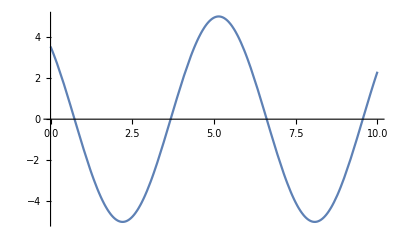

```mathematica
Clear[values]
values ={m->1.75, k->2,A->5,ϕ->π/4};
Plot[x[t]/.values, {t,0,10}]
```

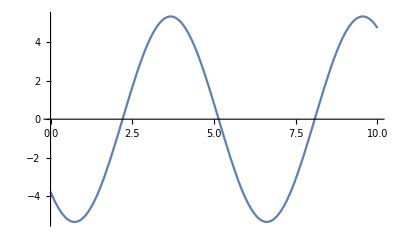

```mathematica
Plot[v[t]/.values,{t,0,10}]
```

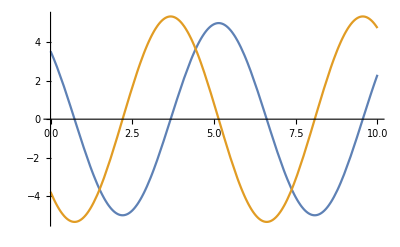

```mathematica
Plot[{x[t]/.values, v[t]/.values},{t,0,10}]
```

```mathematica
(* As funções x(t) e v(t) já foram definidas; não é necessário reescrevê-las *)
A:=√(Subscript[x, 0]^2+(Subscript[v, 0]/ω)^2);
ϕ:=ArcTan[-Subscript[v, 0]/(ω*Subscript[x, 0])];
```

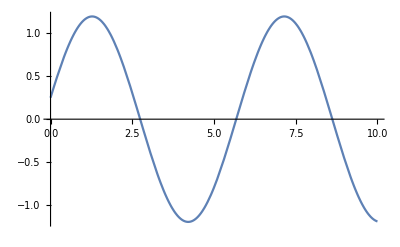

```mathematica
Clear[values];
values = {m->1.75, k->2,Subscript[x, 0] -> 0.25,Subscript[v, 0]->1.25 };
Plot[x[t]/.values,{t,0,10}]
```

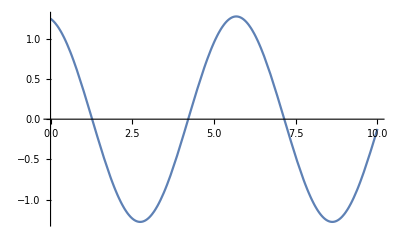

```mathematica
Plot[v[t]/.values,{t,0,10}]
```

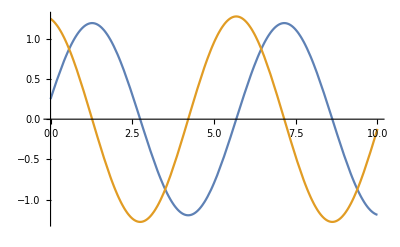

```mathematica
Plot[{x[t]/.values, v[t]/.values},{t,0,10}]
```

```mathematica
K[v_]:=(1/2)m*v^2;
U[x_]:=(1/2)k*x^2;
```

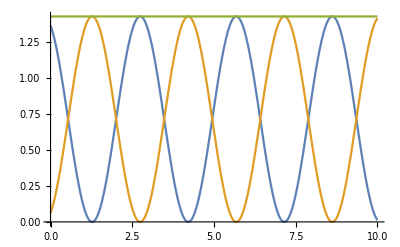

```mathematica
Plot[
{K[v[t]]/.values, U[x[t]]/.values,(K[v[t]]+U[x[t]])/.values},
{t,0,10}
]
```